# Periodic Orbits

## Definitiions

The VDP system has one periodic orbit and the Rosseler system looks like it might have periodic orbits.  First we need to define a periodic orbit and a thing called a winding number.

Orbit of ODE (Informal Definition)
The solution of an ODE y'=f(y) defined by a choice of y(0)=y_0 is called an orbit.

Periodic Orbit of ODE (Informal Definition)
An orbit of the ODE y'=f(y) is periodic if for some T>0 we have  y(t)=y(t+T) for all t.The period is the smallest possible T.

Map (Informal Definition)
A map is function g:ℝ^n→ℝ^n. An orbit is the sequence y_(k+1)=g(y_k) defined by a choice of y_0∈ℝ^n.

Periodic Orbit of Map (Informal Definition)
The orbit y_(k+1)=g(y_k) is periodic if for some K≥1 we have y_k=y_(k+K) for all k.  The period is the smallest possible K.

## Periodic Orbits for VDP

The VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
clearly has a periodic orbit which sucks all the solutions in.  We can approximate a point on this periodic orbit by running the ODE solver and grabbing any value well out in the orbit.

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=64.5;y0={0,0.1};μ=0.2; ϵ=1;
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]]
},2]
```

12

We can estimate the period from a graph.

```mathematica
ySol[TMax]
```

{1.99887,-0.0466208}

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=6.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521}
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax],
GridLines->{Automatic,yPer}]
},2]
```

{1.99887,-0.0466208}

12

We can compute it accurately using a variety of numerical tricks.

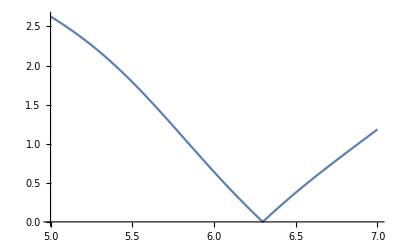

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=7.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
Plot[Norm[ySol[t]-yPer],{t,5,7}]
```

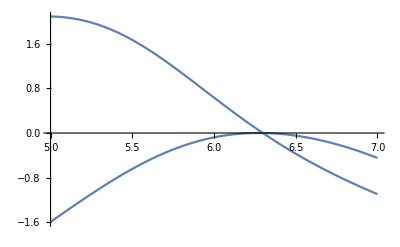

```mathematica
Plot[ySol[t]-yPer,{t,5,7}]
```

```mathematica
tSub=FindRoot[ySol[t][[2]]==yPer[[2]], {t, 6.2}]
ySol[t]/.tSub
yPer
```

Part::partw: Part 2 of InterpolatingFunction[{{0.,7.2}},{5,3,1,{125},{4},0,0,0,0,Automatic,«3»},{{0.,0.0000766691,0.000153338,«6»,0.051148,«115»}},{{{1.99887,-0.0466208},{-0.0466208,-1.97094}},{{1.99886,-0.0467719},{-0.0467719,-1.97084}},«7»,{{1.99393,-0.145807},{-0.145807,-1.90715}},«115»},{Automatic}][t] does not exist.

{t→6.29869}

{1.99958,-0.0466208}

{1.99887,-0.0466208}

Another way to do this is using the EventLocator

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=7.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==yPer⟦2⟧,Direction->-1,"EventAction":> Print[t]}]
```

Part::partw: Part 2 of y[t] does not exist.

6.29869

InterpolatingFunction[…]

Are there any other periodic orbits?  We are going to talk about this in class.

## Periodic orbits for the Rosseller System

As we saw before, there seem to be a lot of near misses for periodic orbits.  Are there periodic orbits?  There are a lot of things we don’t  know when searching for a periodic orbit: where it starts and stops y_0 and the period T.

One way to find periodic a periodic orbit is to start with a near miss. We can probably find a near miss if we mess around down near the flat bit of the “attractor”.

I really did get what is below just messing around!  There is something very close to a periodic orbit here because it looks like the curves merge.  In a top view you can see that it is close but not perfect.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
StdParams={0.2,0.2,5.7};  TMax=25.0;
y0={4.98,5.01,1};
ySol=NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==y0},y,{t,0, TMax}];
CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
Manipulate[
Show[CurvePic,
Graphics3D[{PointSize[0.03],{Red, Point[ySol[t1]]},{Cyan, Point[ySol[t2]]}}],
PlotLabel->{ySol[t1],ySol[t2]}],
{{t1,0}, 0, TMax},
{{t2,TMax/2}, 0, TMax}
]
```

We can isolate the near miss part and make a function that will let is tweak the starting point. We can then fix the “almost” part by tweaking the values carefully. Right now there are four things (the three starting coordinates {y_1,y_2,y_3} and the time “t” to tweak.  The  cross-section idea will reduce this to two!

```mathematica
TMax=14;
ySolPar=ParametricNDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]=={y1,y2,y3}},y,{t,0, TMax},{y1,y2,y3}];
ParametricPlot3D[ySolPar[-2.95,3.45,0.025][t],{t,0, TMax},PlotRange->All]
```

-Graphics3D-

```mathematica
FindRoot[ySol[{y1,y2,y3}][t]=={y1,y2,y3},
{{t,12,7,TMax},{y1,-2.95},{y2,3.45},{y3,0.025}}]
```

InterpolatingFunction::dmval: Input value {-2.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {«1»} is not a list of numbers with dimensions {3} at {t,y1,y2,y3} = {12.,-2.95,3.45,0.025}.

FindRoot[ySol[{y1,y2,y3}][t]=={y1,y2,y3},{{t,12,7,TMax},{y1,-2.95},{y2,3.45},{y3,0.025}}]

```mathematica
?FindRoot
```

```mathematica
ySol[TMax]
```

{-2.03295,3.55781,0.30814}